```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

MeanFirstPassageTimeSet[Q_,start_,hit_]:=Module[{n,l,subIdxs,Qsub,rhs,x},
n=Length[Q];
l = Length[hit];
If[MemberQ[hit,start],(*If same state,MFPT=0 by definition*)
(*Else i!=j,solve the submatrix system:*)
T=0,
subIdxs=Delete[Range[n],hit];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,Length[subIdxs]];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T=x[[First@Position[subIdxs,start]]];];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]+s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

(*Function to estimate c using the method of moments*)
EstimateC[sampleMean_,trueMean_]:=Module[{c},
Return[c/. Solve[trueMean==sampleMean,c]];];

(*Function to compute the variance of the estimator for c*)
VarianceEstimatorC[varianceSample_,edges_,weights_,n_,targetStates_]:=Module[{Q,V,cVar},Q=RateMatrix[edges,weights,n];
V=VarianceFirstPassageTimes[Q];
cVar/. Solve[V[[Sequence@@targetStates]]==varianceSample,cVar]];
```

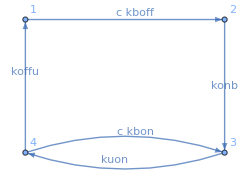

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Pure ligand, 1 binding site ***)

(*Edge lists and weights*)
edges1={{1,2},{2,3},{3,4},{4,3},{4,1}};
weights1={c*kboff,konb,kuon,c*kbon,koffu};
nstates1 = 4;
nedges1 = 5;

(*Plot the circuit*)
edgeList=Table[edges1[[i,1]]->edges1[[i,2]],{i,1,nedges1}];
g=Graph[edges1,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights1)[[i]],0.55],{i,1,nedges1}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{4,1},{3,2}}}]
```

```mathematica
Q1= RateMatrix[edges1, weights1, nstates1];
ss1 = SteadyStateProbabilities[Q1];

(*Mean first passage times*)
meanToff=MeanFirstPassageTimes2[Q1][[1,3]][[1]];
meanTon = MeanFirstPassageTimes2[Q1][[3,1]][[1]];
tau = meanToff + meanTon;

(*Variance of first passage times*)
varToff = FullSimplify[VarianceFirstPassageTimes[Q1][[1,3]]][[1]][[1]];
varTon = FullSimplify[VarianceFirstPassageTimes[Q1][[3,1]]][[1]][[1]];
```

```mathematica
(*MM estimators*)
cHatOff = c/.Solve[meanToff==sampleToff,c][[1]];
cHatOn = c/.Solve[meanTon==sampleTon,c][[1]];

(*Variances of estimators*)
VarCHatOff = Simplify[With[{sampleToff = meanToff}, Evaluate[D[cHatOff, {sampleToff,1}]^2]]*varToff];
VarCHatOn = Simplify[With[{sampleTon = meanTon}, Evaluate[D[cHatOn, {sampleTon,1}]^2]]*varTon];
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
dotFoff = FullSimplify[c^2 / (tau*VarCHatOff)];
dotFon = FullSimplify[c^2 / (tau*VarCHatOn)];
dotF = dotFoff + dotFon;
```

```mathematica
(*Maximize Fisher information rate*)
NMaximize[{With[{c=50},Evaluate[dotFoff]],0<kboff<0.0888,0<konb<5,0<kuon<5,0<kbon<0.0888,0<koffu<5 },{kboff,konb,kuon,kbon,koffu}]
```

{0.8,{kboff→0.05,konb→5.,kuon→5.,kbon→-9.9875×10^-9,koffu→5.}}

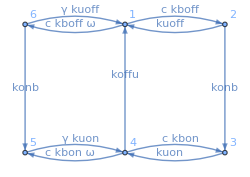

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},{4,5},{5,4},{6,5},{4,1},{2,3}};
weights2={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb};
nstates2 = 6;
nedges2 = Length[edges2];

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];

(*Mean first passage times*)
meanToff=MeanFirstPassageTimeSet[Q2][[1,{{5},{3}}]][[1]]; 
meanT31 = MeanFirstPassageTimes2[Q2][[3,1]][[1]];
meanT51 = MeanFirstPassageTimes2[Q2][[5,1]][[1]];
meanTon = ss2[[2]]*Q2[[2,3]]*meanT31 + ss2[[6]]*Q2[[6,5]]*meanT51;
tau = meanToff + meanTon;

(*Variance of first passage times*)
varT31 = FullSimplify[VarianceFirstPassageTimes[Q2][[3,1]]][[1]][[1]];
varT51 = FullSimplify[VarianceFirstPassageTimes[Q2][[5,1]]][[1]][[1]];
varTon = (ss2[[2]]*Q2[[2,3]])^2*varT31 + (ss2[[6]]*Q2[[6,5]])^2*varT51
```

```mathematica
(*Laplace transform of FPTs*)
F13 = LaplaceTransformFPT[Q2,s1][[1,3]][[1]];
F31 = LaplaceTransformFPT[Q2,s2][[3,1]][[1]];
F15 = LaplaceTransformFPT[Q2,s1][[1,5]][[1]];
F51 = LaplaceTransformFPT[Q2,s2][[5,1]][[1]];
Fjoint = F13*F31 + F15*F51;
F = Fjoint;

(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = -With[{s1=0, s2=0}, Evaluate[D[F, {s1,1}]]];
partials2 = -With[{s1=0, s2=0}, Evaluate[D[F, {s2,1}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[F, {s2,1}],{s1,1}]]];
(*Var = FullSimplify[sndMom - fstMom^2]*)
Cov = FullSimplify[partials1s2 - partials1*partials2]
```

```mathematica
(*MM estimators*)
cHatOff = c/.Solve[meanToff==sampleToff,c][[1]];
cHatOn = c/.Solve[meanTon==sampleTon,c][[1]];

(*Variances of estimators*)
VarCHatOff = Simplify[With[{sampleToff = meanToff}, Evaluate[D[cHatOff, {sampleToff,1}]^2]]*varToff];
VarCHatOn = Simplify[With[{sampleTon = meanTon}, Evaluate[D[cHatOn, {sampleTon,1}]^2]]*varTon];
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
dotFoff = FullSimplify[c^2 / (tau*VarCHatOff)];
dotFon = FullSimplify[c^2 / (tau*VarCHatOn)];
dotF = dotFoff + dotFon;
```

```mathematica
(*Maximize Fisher information rate*)
NMaximize[{With[{c=50},Evaluate[dotF]],0<kboff<0.0888,0<konb<5,0<kuon<5,0<kbon<0.0888,0<koffu<5 },{kboff,konb,kuon,kbon,koffu}]
```

{0.8,{kboff→0.05,konb→5.,kuon→5.,kbon→-9.95197×10^-9,koffu→5.}}

```mathematica
(*Covariance of estimator*)
```

```mathematica
(*Linear combination of two correlated estimators*)
```

```mathematica
(*Covariance matrix of estimators*)
Σ ={{σ1^2,ρ*σ1*σ2},{ρ*σ1*σ2, σ2^2}}
```

{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}}

```mathematica
(*Hessian*)
invΣ = Inverse[Σ]
```

{{σ2^2/(σ1^2 σ2^2-ρ^2 σ1^2 σ2^2),-(ρ σ1 σ2)/(σ1^2 σ2^2-ρ^2 σ1^2 σ2^2)},{-(ρ σ1 σ2)/(σ1^2 σ2^2-ρ^2 σ1^2 σ2^2),σ1^2/(σ1^2 σ2^2-ρ^2 σ1^2 σ2^2)}}

```mathematica
Simplify[%*(1-ρ^2)]
```

{{1/σ1^2,-ρ/(σ1 σ2)},{-ρ/(σ1 σ2),1/σ2^2}}

```mathematica
(Σ.Σ)[[1,1]]
```

σ1^4+ρ^2 σ1^2 σ2^2